# Math Boot Camp: Integration

You can skip this boot camp if you can answer the following questions:

Example
What is the line integral of 1/r^2 r̂ along a radial path starting from r=∞ and ending at r=R?

Example
Prove that the volume of a cone with base radius R and height H is V=1/3 π R^2 H.

### Line Integral

A line integral is an expression of the form

∫_𝒫 v⃗·ⅆ l⃗

where v⃗ is a vector function, ⅆ l⃗ is the infinitesimal displacement vector, and the integral is to be carried out along a prescribed path 𝒫. If the path 𝒫 forms a closed loop (i.e. its two endpoints are the same), the line integral is often written as

∮ v⃗·ⅆ l⃗

At each point on the path we take the dot product of v⃗ (evaluated at that point) with the displacement ⅆ l⃗ to the next point on the path. A familiar example of a line integral is the work done by a force F⃗: W=∫F⃗·ⅆ l⃗.

Example
Calculate the line integral of the function v⃗=y^2 x̂+2x (y+1)ŷ from the point a⃗=(1,1,0) to the point b⃗=(2,2,0) along the path (1) and (2) in the figure below. What is ∮ v⃗·ⅆ l⃗ for the loop that goes from a⃗ to b⃗ along (1) and then returns along (2)?

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Solution
As always, ⅆ l⃗=(ⅆx)x̂+(ⅆy)ŷ+(ⅆz)ẑ. Path 1 consists of two parts: part (i) is a horizontal line segment spanning x∈[1,2] where ⅆy=ⅆz=0. Thus ⅆ l⃗=(ⅆx)x̂ and y=1 so that v⃗·ⅆ l⃗=(x̂+4x ŷ)·(ⅆx)x̂=ⅆx and hence

∫_(i) v⃗·ⅆ l⃗=∫_1^2 ⅆx=1

On the vertical stretch (ii) of this path, y∈[1,2] while ⅆx=ⅆz=0 and x=2 so that ⅆ l⃗=(ⅆy)ŷ and v⃗·ⅆ l⃗=(y^2 x̂+4(y+1)ŷ)·(ⅆy)ŷ=4(y+1)ⅆy. Therefore

∫_(ii) v⃗·ⅆ l⃗=∫_1^2 4(y+1)ⅆy=10

Putting the two paths together, we find that along path (1),

∫_(1) v⃗·ⅆ l⃗=∫_(i) v⃗·ⅆ l⃗+∫_(ii) v⃗·ⅆ l⃗=11

On path (2), define t as a variable that spans t∈[1,2], so that x=y=t along path (2). Then ⅆx=ⅆy=ⅆt and ⅆz=0 so that ⅆ l⃗=(ⅆt)x̂+(ⅆt)ŷ and v⃗·ⅆ l⃗=(t^2 x̂+2t (t+1)ŷ)·((ⅆt)x̂+(ⅆt)ŷ)=(3 t^2+2t)ⅆt. Thus the path integral equals

∫_(2) v⃗·ⅆ l⃗=∫_1^2 3 t^2+2tⅆt=10

Going backwards along a path amounts to flipping the direction of integration, which amounts to a change in the sign of the line integral. Thus, for the loop that goes out through (1) and comes back through path (2),

∮ v⃗·ⅆ l⃗=∫_(1) v⃗·ⅆ l⃗-∫_(2) v⃗·ⅆ l⃗=1

If we considered the full loop in the reverse direction (out through path (2) and back through path (1)) then we would have gotten the negative of this answer, so make sure to keep your orientation straight! □

Example
What is the line integral of 1/r^2 r̂ along a radial path starting from r=∞ and ending at r=R?

Solution
Call the result of the line integral L. Just for clarity (since it is always easiest to visualize positive numbers), we shall integrate along the reverse path starting from r=R and going out to r=∞ to obtain -L, and then take the negative of the result. We will define the radial coordinate s that keeps track of how far the particle is from the origin and let it vary as s∈[R,∞],

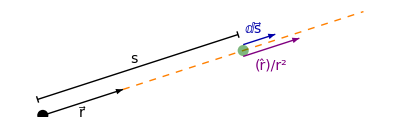

```mathematica
p={Cos[π/10],Sin[π/10]};pPerp=RotationMatrix[π/2].p;origin={0,0};
{a1,a2}={0.2,0.2};
centerPlot@Graphics[{Arrowheads[0.03],PointSize[0.02],Point[origin],Arrow[{origin,p}],{Dashed,Orange,Line[{p,4p}]},{Line[{{origin+a1 pPerp,2.5p+a1 pPerp},{(1+a2)a1 pPerp,(1-a2)a1 pPerp},{2.5p+(1+a2)a1 pPerp,2.5p+(1-a2)a1 pPerp}(*,{2.52p+(1+a2)a1 pPerp,2.52p+(1-a2)a1 pPerp}*)(*,{2.52p+a1 pPerp,2.7p+a1 pPerp}*)(*,{2.7p+(1+a2)a1 pPerp,2.7p+(1-a2)a1 pPerp}*)}]},{Darker@Darker@Green,Opacity[0.5],Point[2.5p]},Text[font["r⃗",14],p/2+{0,-0.12}],{Darker@Blue,Arrow[#+{0,0.07}&/@{2.5p,2.9p}],Text[font["ⅆs⃗",14],2.7p+{-0.07,0.2}]},{Purple,Arrow[#+{0,-0.07}&/@{2.5p,3.2p}],Text[font["(r̂)/r^2",14],2.85p+{0.0,-0.3}]},Text[font["s",Italic,14],1.25p+a1 pPerp+{-0.05,0.1}]}]
```

Taking the dot product of our function 1/s^2 r̂ along with the direction vector ⅆ s⃗=ⅆs r̂ along the line integral, we compute

-L=∫_R^∞ 1/s^2 ⅆs=1/R

so that

L=-1/R

It makes sense that the result is negative, since if we think about the original integral, the direction of the path from ∞ to R points inward, which is opposite of the direction 1/r^2 r̂, and hence we are integrating over purely negative quantities which must give a negative result. We will come back to this specific line integral when computing the electric potential of a point charge. □

### Surface Integral

A surface integral is an expression of the form

∫_S v⃗·ⅆ a⃗

where v⃗ is again some vector function, and ⅆ a⃗ is an infinitesimal patch of area, with direction perpendicular to the surface, as shown in the figure below.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

There are, of course, two directions perpendicular to any surface, so the sign of a surface integral is intrinsically ambiguous. If the surface is closed (forming a "balloon"), then a surface integral may be written as

∮ v⃗·ⅆ a⃗

By convention, the direction "outward" is treated as positive for closed surfaces, but for open surfaces the sign of the answer is arbitrary. If v⃗ describes the flow of a fluid (mass per unit area per unit time), then ∫_S v⃗·ⅆ a⃗ represents the total mass per unit time passing through the surface - hence its alternative name, “flux.”

Example
Calculate the surface integral of v⃗=2x z x̂+(x+2)ŷ+y (z^2-3)ẑ over the square area shown below bounded by the points (2,0,0),(2,2,0),(2,2,2),and (2,0,2). Let the direction +x̂ denote the positive direction.

```mathematica
centerPlot@Show[Plot3D[0,{x,0,2},{y,0,2},PlotStyle->None,AspectRatio->1,PlotRange->{{0,3},{0,2},{0,2}},ViewPoint->{1.9628316520553186,-2.5085014343800793,1.1422401058458904},Mesh->None,AxesLabel->{x,y,z},ImageSize->200],Graphics3D[{Polygon[{{2,0,0},{2,2,0},{2,2,2},{2,0,2}}],Darker@Darker@Green,Arrow[{{2,1,1},{3,1,1}}]}]]
```

-Graphics3D-

Solution
For this surface, x=2 and ⅆ a⃗=ⅆyⅆz x̂ so that v⃗·ⅆ a⃗=4zⅆyⅆz. Therefore, the surface integral equals

∫_S v⃗·ⅆ a⃗=∫_0^2 ∫_0^2 4zⅆyⅆz=16

Had we chosen the -x̂ to denote the positive direction for the integral, we would have found the negative of this answer. □

### Volume Integral

A volume integral is an expression of the form

∫_𝒱 Tⅆτ

where T is a scalar function and ⅆτ is an infinitesimal volume element. In Cartesian coordinates,

ⅆτ=ⅆxⅆyⅆz

For example, if T is the density of a substance (which might vary from point to point), then the volume integral would give the total mass. You can also take the volume integral of a vector function

∫_𝒱 A⃗ ⅆτ=x̂∫_𝒱 A_x ⅆτ+ŷ∫_𝒱 A_y ⅆτ+ẑ∫_𝒱 A_z ⅆτ

where the unit vectors come outside the integrals because they are constant.

Example
Calculate the volume integral of T=x y z^2 over the prism shown below.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Solution
This is just plain calculus, but you need to keep track of your variable ranges carefully to ensure that you cover the entire figure. You can take the integrals in any order (and doing a problem in multiple ways is often a great way to check your work). In this case, we will do the x integration first, which spans the range x∈[0,1-y]. After that, we do the y integration along the range y∈[0,1] and the z integration along z∈[0,3]. Thus, the integral is given by

∫_𝒱 Tⅆτ=∫_0^3 z^2{∫_0^1 y(∫_0^(1-y) xⅆx)ⅆy}ⅆz
=∫_0^3 z^2{∫_0^1 1/2 y (y-1)^2 ⅆy}ⅆz
=∫_0^3 1/24 z^2 ⅆz
=3/8

which is the desired answer. □

Example
Most people know that the volume of a cone with base radius R and height H is V=1/3 π R^2 H. Prove this for a right cone whose base of radius R is centered about (0,0,0) and whose apex is at (0,0,H).

Note: In the Volume Elements bootcamp we prove this formula much more easily by using spherical coordinates. But sometimes, a little pain is good for you.

```mathematica
ft=16;
centerPlot@Graphics3D[{Opacity[0.6],Cone[],Line[{{{0,0,-1},{0,0,1}},{{0,0,-1},{1,0,-1}}}],Text[font["H",Italic],{-0.15,0,0}],Text[font["R",Italic],{0.45,0.1,-0.93}]},ViewPoint->{0.,-3,0.3},Boxed->False,ImageSize->200]
```

-Graphics3D-

Solution
The volume equals the volume integral of the constant function 1 over the entire cone. We will take slices of thickness ⅆz along the z-axis. First, we integrate the x and y variables across these slices, and finally we will integrate z across its span z∈[0,H]. At any given height z, the corresponding slice will be a thin cylinder with radius (1-z/H)R, and therefore the y integration spans [-(1-z/H)R,(1-z/H)R]. Finally, at any given z and y, the x integration spans [-{(1-z/H)^2 R^2-y^2}^(1/2),{(1-z/H)^2 R^2-y^2}^(1/2)]. Therefore, the volume of the cone is given by

V=∫_0^H ∫_(-(1-z/H)R)^((1-z/H)R) ∫_(-{(1-z/H)^2 R^2-y^2}^(1/2))^({(1-z/H)^2 R^2-y^2}^(1/2)) ⅆxⅆyⅆz
=∫_0^H π (1-z/H)^2 R^2 ⅆz
=1/3 π R^2 H^3

We could also be a bit more clever and know that the slices will be (to first order) cylinders with radius (1-z/H)R and height ⅆz, which must have volume π (1-z/H)^2 R^2 ⅆz, and thus skip to the second step. Alternatively, we can be cleverer still and do the calculation in Mathematica,

```mathematica
Integrate[1,{z,0,H},{y,-(1-z/H)R,(1-z/H)R},{x,-√((1-z/H)^2 R^2-y^2),√((1-z/H)^2 R^2-y^2)},Assumptions->0<H&&0<R]
```

1/3 H π R^2

A very similar calculation shows that the volume of any prism with base area A and height H has volume 1/3 A H. If we orient the prism so that its base lies at z=0 and its tip at z=H, then from the second line in (TextNumbered) we find that its area at height z∈[0,H] equals A (1-z/H)^2. (One factor of (1-z/H) comes from contracting the base in the x-direction and another from contracting the base in the y-direction.) Therefore the volume equals

V=∫_0^H A (1-z/H)^2 ⅆz
=1/3 A H

as desired. □

## Mathematica Initialization

```mathematica
Clear[font]
font[text_,size_Integer:14,opts___]:=(Style[text,size,FontFamily->"Times",opts])
```